```mathematica
Quit[]
```

```mathematica
rawdata =Import["/Users/stevenschowalter/Desktop/phys191mms/HeData/mms_copper_312run8.txt","Table"];
```

```mathematica
num=Dimensions[rawdata][[1]];
```

```mathematica
temp=Table[0,{i,num}];
```

```mathematica
time=Take[rawdata,All,{3}];
voltage=Take[rawdata,All,{2}];
pulse=Take[rawdata,All,{1}];
```

```mathematica
Do[temp[[i]]=ⅇ^(-0.004995*Log[1000*voltage[[i]]]^3+0.1314*Log[1000*voltage[[i]]]^2-1.43Log[1000*voltage[[i]]]+5.92),{i,1,num}];
```

```mathematica
timetemp=Table[0,{i,num}];
Do[timetemp[[i]]=Flatten[{time[[i]],temp[[i]]},2],{i,1,num}]
```

```mathematica
timevolt=Table[0,{i,num}];
Do[timevolt[[i]]=Flatten[{time[[i]],voltage[[i]]},2],{i,1,num}]
```

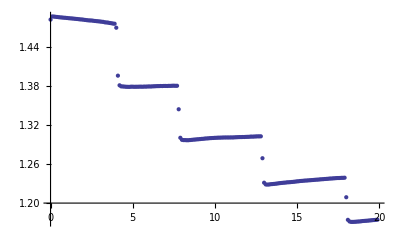

```mathematica
ListPlot[Take[timevolt,{1,200}]]
```

```mathematica
threshold=.005;
dT={};
Do[If[voltage[[i+2]][[1]]<voltage[[i]][[1]]-threshold,{dT=Join[dT,{{voltage[[i]][[1]],Mean[Take[voltage,{i-5,i}]][[1]]-Mean[Take[voltage,{i+3,i+7}]][[1]]}}]}],{i,num-7}]
```

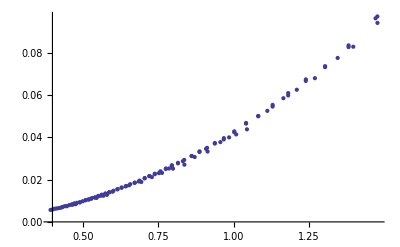

```mathematica
ListPlot[dT]
```

```mathematica
threshold=.005;
dT={};
Do[If[voltage[[i+2]][[1]]<voltage[[i]][[1]]-threshold,{Print[timevolt[[i]]],Print[Mean[Take[voltage,{i-5,i}]]-Mean[Take[voltage,{i+2,i+7}]]],dT=Join[dT,{{voltage[[i]][[1]],Mean[Take[voltage,{i-5,i}]][[1]]-Mean[Take[voltage,{i+2,i+7}]][[1]]}}]}],{i,num-7}]
```

```mathematica
Q=10.5^2/1116 10^-2;
```

```mathematica
threshold=.002;
```

```mathematica
dT={};
Do[If[temp[[i+2]][[1]]>temp[[i]][[1]]+threshold,{dT=Join[dT,{{temp[[i]][[1]],Q/(-Mean[Take[temp,{i-5,i}]][[1]]+Mean[Take[temp,{i+3,i+7}]][[1]])}}]}],{i,num-7}]
```

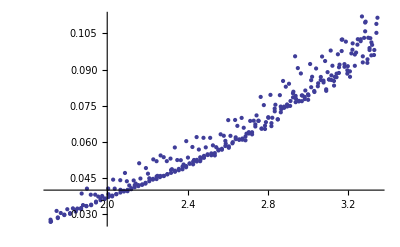

```mathematica
ListPlot[dT]
```

```mathematica
Dimensions[dT]
```

{300,2}

```mathematica
dV=Take[dT,All,{2}];
V=Take[dT,All,{1}];
```

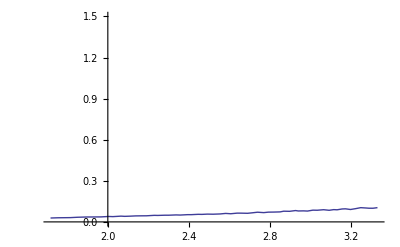

```mathematica
avgsize=5;
avgnum=Quotient[300,avgsize];
avgV=Take[V,{1,-1,avgsize}];
avgdV=Table[0,{i,avgnum}];
Do[avgdV[[i]]=Mean[Take[dV,{1+avgsize(i-1),avgsize(i)}]],{i,1,avgnum}]
avgdT=Table[0,{i,avgnum}];
Do[avgdT[[i]]=Flatten[{avgV[[i]],avgdV[[i]]},2],{i,1,avgnum}]
ListPlot[avgdT,PlotRange->{0,1.5},Joined->True]
```

```mathematica
Needs["NonlinearRegression`"]
```